```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(κ+k)/γ,κ/γ},{κ/γ,-κ/γ}}
```

{{(-k-κ)/γ,κ/γ},{κ/γ,-κ/γ}}

```mathematica
MatrixForm[M]
```

((-k-κ)/γ | κ/γ
κ/γ | -κ/γ)

```mathematica
expM=MatrixExp[M*(-tp)]
```

{{-(ⅇ^((tp (k+2 κ-√(k^2+4 κ^2)))/(2 γ)) (k-√(k^2+4 κ^2)))/(2 √(k^2+4 κ^2))+(ⅇ^((tp (k+2 κ+√(k^2+4 κ^2)))/(2 γ)) (k+√(k^2+4 κ^2)))/(2 √(k^2+4 κ^2)),(ⅇ^((tp (k+2 κ-√(k^2+4 κ^2)))/(2 γ)) κ)/(√(k^2+4 κ^2))-(ⅇ^((tp (k+2 κ+√(k^2+4 κ^2)))/(2 γ)) κ)/(√(k^2+4 κ^2))},{(ⅇ^((tp (k+2 κ-√(k^2+4 κ^2)))/(2 γ)) κ)/(√(k^2+4 κ^2))-(ⅇ^((tp (k+2 κ+√(k^2+4 κ^2)))/(2 γ)) κ)/(√(k^2+4 κ^2)),-(ⅇ^((tp (k+2 κ-√(k^2+4 κ^2)))/(2 γ)) (-k-√(k^2+4 κ^2)))/(2 √(k^2+4 κ^2))+(ⅇ^((tp (k+2 κ+√(k^2+4 κ^2)))/(2 γ)) (-k+√(k^2+4 κ^2)))/(2 √(k^2+4 κ^2))}}

```mathematica
covar=Integrate[expM.{{2*Subscript[T, c]/γ,0},{0,2*Subscript[T, h]/γ}}.Transpose[expM],{tp,-Infinity,0},Assumptions->{γ>0,k>0,κ>0}]
```

{{((k+κ) T_c+κ T_h)/(k (k+2 κ)),(κ T_c+(k+κ) T_h)/(k (k+2 κ))},{(κ T_c+(k+κ) T_h)/(k (k+2 κ)),(κ^2 T_c+(k^2+3 k κ+κ^2) T_h)/(k κ (k+2 κ))}}

```mathematica
FullSimplify[covar/.{Subscript[T, c]->Subscript[T, h]},Assumptions->{γ>0,k>0,κ>0}]
```

{{T_h/k,T_h/k},{T_h/k,((k+κ) T_h)/(k κ)}}

```mathematica
P[x_,y_,kk_]:=Simplify[Exp[-1/2*{x,y}.Inverse[covar].{x,y}]]/.{k->kk}
```

```mathematica
Log[P[x,y,k]]
```

Log[ⅇ^(-((k+2 κ) (κ (k y^2+(x-y)^2 κ) T_c+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) T_h))/(2 (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2)))]

```mathematica
expo = -((k+2 κ) (κ (k y^2+(x-y)^2 κ) Subscript[T, c]+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) Subscript[T, h]))/(2 (κ^2 Subscript[T, c]^2+(k^2+4 k κ+2 κ^2) Subscript[T, c] Subscript[T, h]+κ^2 Subscript[T, h]^2))
```

-((k+2 κ) (κ (k y^2+(x-y)^2 κ) T_c+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) T_h))/(2 (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2
```

(2 U_0)/L^2

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2
```

(2 U_0)/l^2

```mathematica
SubMinus[f]=FullSimplify[Integrate[P[x,y,SubMinus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

ⅇ^(-(2 x^2 U_0 (L^2 κ+U_0))/(L^4 κ (T_c+T_h)+2 L^2 T_c U_0)) √π √((L^4 κ^2 (T_c+T_h)^2+8 L^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (L^2 κ+U_0) (L^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
FullSimplify[Limit[SubMinus[f],x->0],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

√π √((L^4 κ^2 (T_c+T_h)^2+8 L^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (L^2 κ+U_0) (L^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
SubPlus[f]=FullSimplify[Integrate[P[x,y,SubPlus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

ⅇ^(-(2 x^2 U_0 (l^2 κ+U_0))/(l^4 κ (T_c+T_h)+2 l^2 T_c U_0)) √π √((l^4 κ^2 (T_c+T_h)^2+8 l^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (l^2 κ+U_0) (l^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
FullSimplify[Limit[SubPlus[f],x->0],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

√π √((l^4 κ^2 (T_c+T_h)^2+8 l^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (l^2 κ+U_0) (l^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{x->0})==SubPlus[A]*(SubPlus[f]/.{x->0})&&SubMinus[A]*Integrate[SubMinus[f],{x,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]+SubPlus[A]*Integrate[SubPlus[f],{x,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{A_-→(2 √2 U_0 (L^2 κ+U_0) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))))/(l L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0))))),A_+→(2 √2 U_0 (l^2 κ+U_0) √((κ (L^2 κ+U_0))/((l^6 κ^2 (T_c+T_h)^2+8 l^4 κ T_c T_h U_0+4 l^2 T_c T_h U_0^2) (L^2 κ T_h+T_c (L^2 κ+2 U_0)))))/(L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0)))))}}

## Current

```mathematica
Subscript[J, R] = Simplify[-(k*x+κ*(x-y))/γ*P[x,y,k]-Subscript[T, c]/γ*D[P[x,y,k],x],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

-((ⅇ^(-((k+2 κ) (κ (k y^2+(x-y)^2 κ) T_c+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) T_h))/(2 (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))) κ^2 (T_c-T_h) ((k y+(-x+y) κ) T_c-(k x+(x-y) κ) T_h))/(γ (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2)))

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->l,k->SubPlus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{y→(l^3 κ (T_c+T_h)+2 l T_h U_0)/(l^2 κ (T_c+T_h)+2 T_c U_0)}}

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->-L,k->SubMinus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{y→-(L^3 κ (T_c+T_h)+2 L T_h U_0)/(L^2 κ (T_c+T_h)+2 T_c U_0)}}

```mathematica
Subscript[J, right]=Simplify[Integrate[SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]},{y,y/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

(√2 ⅇ^(-(2 U_0 (l^2 κ+U_0))/(l^2 κ T_h+T_c (l^2 κ+2 U_0))) l (-T_c+T_h) U_0 √((L^2 κ+U_0)/(L^2 κ T_h+T_c (L^2 κ+2 U_0))) (κ/(l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))^(3/2) (l^7 √π κ^3 Erf[l (l^2 κ T_c+T_h (l^2 κ+2 U_0)) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] T_c^3 √((κ (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3)))+l^3 κ T_c^2 (l κ+√π Erf[l (l^2 κ T_c+T_h (l^2 κ+2 U_0)) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] T_h (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2) √((κ (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3))))+T_c (2 T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)+l √π Erf[l (l^2 κ T_c+T_h (l^2 κ+2 U_0)) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] T_h^2 (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3) √((κ (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3)))-l^3 √π κ (l^2 κ Erf[l^3 κ^(3/2) T_c √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+l^3 κ^(3/2) T_h √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+2 l T_h U_0 √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] √((κ (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))+(1+Erf[l^3 κ^(3/2) T_c √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+l^3 κ^(3/2) T_h √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+2 l T_h U_0 √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))]) U_0 √((κ (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))+l^2 √((κ^3 (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))-√((κ (l^2 κ+U_0) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/(l^2 κ T_h+T_c (l^2 κ+2 U_0)))))+l T_h (l^3 κ^2 T_h+l^4 √π κ^2 Erf[l (l^2 κ T_c+T_h (l^2 κ+2 U_0)) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] T_h^2 (l^2 κ+2 U_0) √((κ (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3)))+√π (-l^4 κ^2 Erf[l^3 κ^(3/2) T_c √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+l^3 κ^(3/2) T_h √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+2 l T_h U_0 √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] √((κ (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))-l^4 √((κ^5 (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))+l^2 κ √((κ (l^2 κ+U_0) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/(l^2 κ T_h+T_c (l^2 κ+2 U_0)))-2 U_0^2 (κ Erf[l^3 κ^(3/2) T_c √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+l^3 κ^(3/2) T_h √((l^2 κ+U_0)/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))+2 l T_h U_0 √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))))] √((l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2))/(κ (l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))+√((κ (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0)))))+U_0 (-3 l^2 √((κ^3 (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))-3 l^2 Erf[l^3 T_c √((κ^3 (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3)))+T_h (2 l U_0 √((κ (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3)))+l^3 √((κ^3 (l^2 κ+U_0))/(l^6 κ^3 T_h^3+l^4 κ^2 T_c^3 (l^2 κ+2 U_0)+l^2 κ T_c T_h^2 (3 l^4 κ^2+10 l^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 l^6 κ^3+12 l^4 κ^2 U_0+20 l^2 κ U_0^2+8 U_0^3))))] √((κ^3 (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/((l^2 κ+U_0) (l^2 κ T_h+T_c (l^2 κ+2 U_0))))+2 √((κ (l^2 κ+U_0) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))/(l^2 κ T_h+T_c (l^2 κ+2 U_0))))))))/(L π γ (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0)))))

```mathematica
Subscript[J, left]=Simplify[Integrate[SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]},{y,-Infinity,y/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

(√2 ⅇ^(-(2 U_0 (L^2 κ+U_0))/(L^2 κ T_h+T_c (L^2 κ+2 U_0))) L (T_c-T_h) U_0 √((l^2 κ+U_0)/(l^2 κ T_h+T_c (l^2 κ+2 U_0))) (κ/(L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))^(3/2) (L^7 √π κ^3 Erf[L (L^2 κ T_c+T_h (L^2 κ+2 U_0)) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] T_c^3 √((κ (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3)))+L^3 κ T_c^2 (L κ+√π Erf[L (L^2 κ T_c+T_h (L^2 κ+2 U_0)) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] T_h (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2) √((κ (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3))))+T_c (2 T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)+L √π Erf[L (L^2 κ T_c+T_h (L^2 κ+2 U_0)) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] T_h^2 (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3) √((κ (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3)))-L^3 √π κ (L^2 κ Erf[L^3 κ^(3/2) T_c √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+L^3 κ^(3/2) T_h √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+2 L T_h U_0 √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] √((κ (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))+(1+Erf[L^3 κ^(3/2) T_c √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+L^3 κ^(3/2) T_h √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+2 L T_h U_0 √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))]) U_0 √((κ (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))+L^2 √((κ^3 (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))-√((κ (L^2 κ+U_0) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))))+L T_h (L^3 κ^2 T_h+L^4 √π κ^2 Erf[L (L^2 κ T_c+T_h (L^2 κ+2 U_0)) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] T_h^2 (L^2 κ+2 U_0) √((κ (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3)))+√π (-L^4 κ^2 Erf[L^3 κ^(3/2) T_c √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+L^3 κ^(3/2) T_h √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+2 L T_h U_0 √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] √((κ (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))-L^4 √((κ^5 (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))+L^2 κ √((κ (L^2 κ+U_0) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))-2 U_0^2 (κ Erf[L^3 κ^(3/2) T_c √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+L^3 κ^(3/2) T_h √((L^2 κ+U_0)/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))+2 L T_h U_0 √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))))] √((L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2))/(κ (L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))+√((κ (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0)))))+U_0 (-3 L^2 √((κ^3 (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))-3 L^2 Erf[L^3 T_c √((κ^3 (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3)))+T_h (2 L U_0 √((κ (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3)))+L^3 √((κ^3 (L^2 κ+U_0))/(L^6 κ^3 T_h^3+L^4 κ^2 T_c^3 (L^2 κ+2 U_0)+L^2 κ T_c T_h^2 (3 L^4 κ^2+10 L^2 κ U_0+4 U_0^2)+T_c^2 T_h (3 L^6 κ^3+12 L^4 κ^2 U_0+20 L^2 κ U_0^2+8 U_0^3))))] √((κ^3 (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/((L^2 κ+U_0) (L^2 κ T_h+T_c (L^2 κ+2 U_0))))+2 √((κ (L^2 κ+U_0) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))/(L^2 κ T_h+T_c (L^2 κ+2 U_0))))))))/(l π γ (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ T_h+T_c (L^2 κ+2 U_0)))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0)))))

```mathematica
Subscript[J, total]= Simplify[Subscript[J, right]+Subscript[J, left],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Series[Subscript[J, total]/.{Subscript[T, h]->T+δT/2,Subscript[T, c]->T-δT/2},{δT,0,1}];
```

```mathematica
Subscript[J, total]= (√2 ⅇ^(-(2 Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))) l (-Subscript[T, c]+Subscript[T, h]) Subscript[U, 0] √((L^2 κ+Subscript[U, 0])/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))) (κ/(l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))^(3/2) (l^7 √π κ^3 Erf[l (l^2 κ Subscript[T, c]+Subscript[T, h] (l^2 κ+2 Subscript[U, 0])) √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, c]^3 √((κ (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+l^3 κ Subscript[T, c]^2 (l κ+√π Erf[l (l^2 κ Subscript[T, c]+Subscript[T, h] (l^2 κ+2 Subscript[U, 0])) √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h] (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2) √((κ (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3))))+Subscript[T, c] (2 Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)+l √π Erf[l (l^2 κ Subscript[T, c]+Subscript[T, h] (l^2 κ+2 Subscript[U, 0])) √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h]^2 (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3) √((κ (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))-l^3 √π κ (l^2 κ Erf[l^3 κ^(3/2) Subscript[T, c] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+l^3 κ^(3/2) Subscript[T, h] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 l Subscript[T, h] Subscript[U, 0] √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((κ (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))+(1+Erf[l^3 κ^(3/2) Subscript[T, c] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+l^3 κ^(3/2) Subscript[T, h] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 l Subscript[T, h] Subscript[U, 0] √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))]) Subscript[U, 0] √((κ (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))+l^2 √((κ^3 (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))-√((κ (l^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])))))+l Subscript[T, h] (l^3 κ^2 Subscript[T, h]+l^4 √π κ^2 Erf[l (l^2 κ Subscript[T, c]+Subscript[T, h] (l^2 κ+2 Subscript[U, 0])) √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h]^2 (l^2 κ+2 Subscript[U, 0]) √((κ (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+√π (-l^4 κ^2 Erf[l^3 κ^(3/2) Subscript[T, c] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+l^3 κ^(3/2) Subscript[T, h] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 l Subscript[T, h] Subscript[U, 0] √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((κ (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))-l^4 √((κ^5 (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))+l^2 κ √((κ (l^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])))-2 Subscript[U, 0]^2 (κ Erf[l^3 κ^(3/2) Subscript[T, c] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+l^3 κ^(3/2) Subscript[T, h] √((l^2 κ+Subscript[U, 0])/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 l Subscript[T, h] Subscript[U, 0] √((κ (l^2 κ+Subscript[U, 0]))/((l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))/(κ (l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))+√((κ (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0])))))+Subscript[U, 0] (-3 l^2 √((κ^3 (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))-3 l^2 Erf[l^3 Subscript[T, c] √((κ^3 (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+Subscript[T, h] (2 l Subscript[U, 0] √((κ (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+l^3 √((κ^3 (l^2 κ+Subscript[U, 0]))/(l^6 κ^3 Subscript[T, h]^3+l^4 κ^2 Subscript[T, c]^3 (l^2 κ+2 Subscript[U, 0])+l^2 κ Subscript[T, c] Subscript[T, h]^2 (3 l^4 κ^2+10 l^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 l^6 κ^3+12 l^4 κ^2 Subscript[U, 0]+20 l^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3))))] √((κ^3 (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((l^2 κ+Subscript[U, 0]) (l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))+2 √((κ (l^2 κ+Subscript[U, 0]) (l^4 κ^2 Subscript[T, c]^2+l^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (l^4 κ^2+4 l^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))))))))/(L π γ (Erf[√2 √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])))] √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ Subscript[T, h]+Subscript[T, c] (l^4 κ+2 l^2 Subscript[U, 0])))+Erf[√2 √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^2 κ (Subscript[T, c]+Subscript[T, h])+2 Subscript[T, c] Subscript[U, 0]))] √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ Subscript[T, h]+Subscript[T, c] (L^4 κ+2 L^2 Subscript[U, 0])))))+(√2 ⅇ^(-(2 Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))) L (Subscript[T, c]-Subscript[T, h]) Subscript[U, 0] √((l^2 κ+Subscript[U, 0])/(l^2 κ Subscript[T, h]+Subscript[T, c] (l^2 κ+2 Subscript[U, 0]))) (κ/(L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))^(3/2) (L^7 √π κ^3 Erf[L (L^2 κ Subscript[T, c]+Subscript[T, h] (L^2 κ+2 Subscript[U, 0])) √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, c]^3 √((κ (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+L^3 κ Subscript[T, c]^2 (L κ+√π Erf[L (L^2 κ Subscript[T, c]+Subscript[T, h] (L^2 κ+2 Subscript[U, 0])) √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h] (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2) √((κ (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3))))+Subscript[T, c] (2 Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)+L √π Erf[L (L^2 κ Subscript[T, c]+Subscript[T, h] (L^2 κ+2 Subscript[U, 0])) √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h]^2 (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3) √((κ (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))-L^3 √π κ (L^2 κ Erf[L^3 κ^(3/2) Subscript[T, c] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+L^3 κ^(3/2) Subscript[T, h] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 L Subscript[T, h] Subscript[U, 0] √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((κ (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))+(1+Erf[L^3 κ^(3/2) Subscript[T, c] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+L^3 κ^(3/2) Subscript[T, h] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 L Subscript[T, h] Subscript[U, 0] √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))]) Subscript[U, 0] √((κ (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))+L^2 √((κ^3 (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))-√((κ (L^2 κ+Subscript[U, 0]) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])))))+L Subscript[T, h] (L^3 κ^2 Subscript[T, h]+L^4 √π κ^2 Erf[L (L^2 κ Subscript[T, c]+Subscript[T, h] (L^2 κ+2 Subscript[U, 0])) √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] Subscript[T, h]^2 (L^2 κ+2 Subscript[U, 0]) √((κ (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+√π (-L^4 κ^2 Erf[L^3 κ^(3/2) Subscript[T, c] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+L^3 κ^(3/2) Subscript[T, h] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 L Subscript[T, h] Subscript[U, 0] √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((κ (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))-L^4 √((κ^5 (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))+L^2 κ √((κ (L^2 κ+Subscript[U, 0]) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])))-2 Subscript[U, 0]^2 (κ Erf[L^3 κ^(3/2) Subscript[T, c] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+L^3 κ^(3/2) Subscript[T, h] √((L^2 κ+Subscript[U, 0])/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))+2 L Subscript[T, h] Subscript[U, 0] √((κ (L^2 κ+Subscript[U, 0]))/((L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))))] √((L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2))/(κ (L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))+√((κ (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])))))+Subscript[U, 0] (-3 L^2 √((κ^3 (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))-3 L^2 Erf[L^3 Subscript[T, c] √((κ^3 (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+Subscript[T, h] (2 L Subscript[U, 0] √((κ (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3)))+L^3 √((κ^3 (L^2 κ+Subscript[U, 0]))/(L^6 κ^3 Subscript[T, h]^3+L^4 κ^2 Subscript[T, c]^3 (L^2 κ+2 Subscript[U, 0])+L^2 κ Subscript[T, c] Subscript[T, h]^2 (3 L^4 κ^2+10 L^2 κ Subscript[U, 0]+4 Subscript[U, 0]^2)+Subscript[T, c]^2 Subscript[T, h] (3 L^6 κ^3+12 L^4 κ^2 Subscript[U, 0]+20 L^2 κ Subscript[U, 0]^2+8 Subscript[U, 0]^3))))] √((κ^3 (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/((L^2 κ+Subscript[U, 0]) (L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))+2 √((κ (L^2 κ+Subscript[U, 0]) (L^4 κ^2 Subscript[T, c]^2+L^4 κ^2 Subscript[T, h]^2+2 Subscript[T, c] Subscript[T, h] (L^4 κ^2+4 L^2 κ Subscript[U, 0]+2 Subscript[U, 0]^2)))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0]))))))))/(l π γ (Erf[√2 √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^2 κ Subscript[T, h]+Subscript[T, c] (L^2 κ+2 Subscript[U, 0])))] √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ Subscript[T, h]+Subscript[T, c] (l^4 κ+2 l^2 Subscript[U, 0])))+Erf[√2 √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^2 κ (Subscript[T, c]+Subscript[T, h])+2 Subscript[T, c] Subscript[U, 0]))] √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ Subscript[T, h]+Subscript[T, c] (L^4 κ+2 L^2 Subscript[U, 0])))));
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,δ>0,d>0}];
```

```mathematica
Subscript[J, exp]= Simplify[Subscript[J, paper]/.{κ->q*T},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, sub]=Simplify[Subscript[J, unitless]/.{Subscript[U, 0]->1,d->1,Subscript[λ, l]->0.1,Subscript[λ, r]->0.9,γ->1},{κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, subz]= 1/2*Subscript[J, sub]/.{Subscript[T, 1]->0,Subscript[T, 2]->T};
Subscript[J, subn]=1/2*Subscript[J, sub]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T};
```

```mathematica
v1 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
```

```mathematica
v2 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
```

```mathematica
v5 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
```

```mathematica
v10 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
```

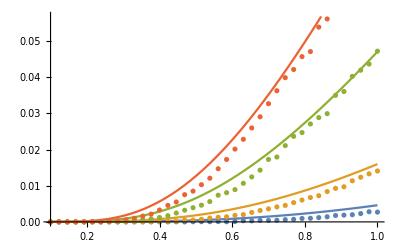

```mathematica
Show[{Plot[{Subscript[J, subn]/.{κ->1},Subscript[J, subn]/.{κ->2},Subscript[J, subn]/.{κ->5},Subscript[J, subn]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1},Transpose@{tvals,-v2},Transpose@{tvals,-v5},Transpose@{tvals,-v10}}]}]
```

```mathematica
v1t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
```

```mathematica
v2t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
```

```mathematica
v5t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
```

```mathematica
v10t0 = Import["/home/data/ie355/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
```

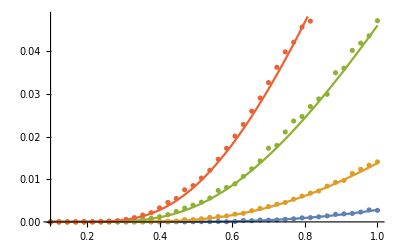

```mathematica
Show[{Plot[{Subscript[J, subz]/.{κ->1},Subscript[J, subz]/.{κ->2},Subscript[J, subz]/.{κ->5},Subscript[J, subz]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t0},Transpose@{tvals,-v2t0},Transpose@{tvals,-v5t0},Transpose@{tvals,-v10t0}}]}]
```